## Exercise Session 6

### Define Henon map

```mathematica
(* Problem 4.3 *)
a=1.4//N;
b=0.3//N;
(* Henon map *)
HM[xy_]:={xy[[2]]+1-a xy[[1]]^2,b xy[[1]]};

J=D[HM[{x,y}],{{x,y}}];
%//MatrixForm
Det[J]
(* use this jacobian for Lyapunov exponent below *)
JM[xy_]:=J/.x->xy[[1]];
(* *)
(* fixed points *)
NSolve[{x,y}==HM[{x,y}],{x,y}]//FullSimplify
fixp=%//N;
```

(-2.8 x | 1
0.3 | 0)

-0.3

{{x→-1.13135,y→-0.339406},{x→0.631354,y→0.189406}}

### Iterate the map

```mathematica
xlim = 2;
ylim=2;
(* interate Henon Map once for a list of input values *)
HenonIt[nlist_]:=Module[{np1list},
np1list=HM/@nlist;
np1list=Cases[np1list,{x_/;Abs[x]≤ xlim,y_/;Abs[y]≤ ylim}] (* remove cases that escape from rectangle with side lengths (3,1) *)
]
```

```mathematica
Nin = 20; (* start with Nin*Nin initial conditions *)
square=Flatten[Table[{i,j},{i,-a,a,2/(Nin-1)},{j,-a b,a b,2/(Nin-1)}],1]//N; (* define a square of intial conditions *)
```

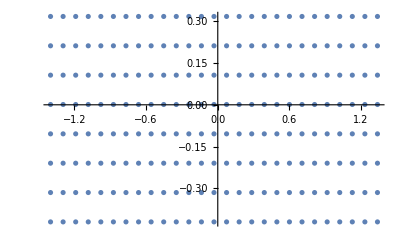

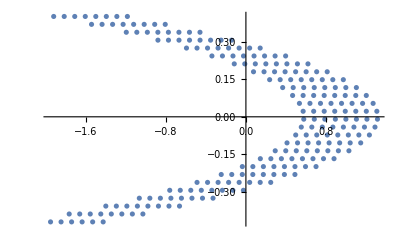

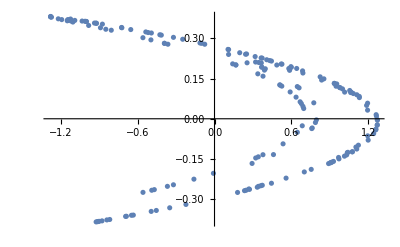

```mathematica
ListPlot[square]
ListPlot[HenonIt[square]] (* Points after one iteration *)
ListPlot[Nest[HenonIt,square,100]](* initial point after 100 interations *)
```

### Example for BinCounts[]

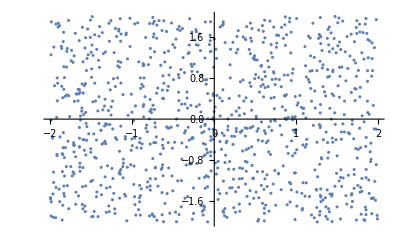

```mathematica
(* take an example orbit, these are 1000 random number pairs *)
orbit = RandomReal[{-2,2},{1000,2}];
ListPlot[orbit]
```

```mathematica
(* put the numbers in to boxes of size ϵ using BinCounts[], flatten the list and remove empty boxes *)
Ntable[ϵ_] :=Cases[BinCounts[orbit,{-b,b,ϵ},{-a*b,a*b,ϵ}]//Flatten,Except[0]]//N;
(* Calculate the probabilities by dividing by the total number of counts*)
Probs[ϵ_]:=Ntable[ϵ]/Plus@@Ntable[ϵ];
(* evaluate the counting and probability functions *)
Ntable[0.1];
Probs[0.1];
```